```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

## Require decay product to enter the trackers

```mathematica
datatracker={Log[10,#1], #2} & @@@ Import[NotebookDirectory[]<>"tracker.csv"][[2;;]]
```

{{-2.69897,0.430209},{-2.61979,0.509677},{-2.55284,0.607149},{-2.48149,0.68654},{-2.39794,0.761685},{-2.3279,0.838338},{-2.25181,0.898864},{-2.18046,0.926326},{-2.10237,0.950054},{-2.02687,0.975629},{-1.95468,0.984714},{-1.87943,0.992543},{-1.8041,0.992339},{-1.73049,0.996506},{-1.65561,0.999263},{-1.5817,0.998745},{-1.50585,1.},{-1.4318,0.999758},{-1.35754,0.999555},{-1.28316,1.},{-1.20831,0.999534},{-1.13371,0.998885},{-1.05948,1.},{-0.98464,1.},{-0.910095,0.998542},{-0.835647,1.},{-0.761201,1.},{-0.686766,1.}}

```mathematica
dataECAL = {Log[10,#1], #4} & @@@ Import[NotebookDirectory[]<>"ECAL.csv"][[2;;]]
```

{{-2.69897,0.0178534},{-2.61979,0.0241575},{-2.55284,0.0305059},{-2.48149,0.039222},{-2.39794,0.0503565},{-2.3279,0.0636734},{-2.25181,0.0804456},{-2.18046,0.107136},{-2.10237,0.144965},{-2.02687,0.192624},{-1.95468,0.252203},{-1.87943,0.326815},{-1.8041,0.410241},{-1.73049,0.492306},{-1.65561,0.566237},{-1.5817,0.622252},{-1.50585,0.665144},{-1.4318,0.694606},{-1.35754,0.708287},{-1.28316,0.70865},{-1.20831,0.699134},{-1.13371,0.680848},{-1.05948,0.655501},{-0.98464,0.618193},{-0.910095,0.575164},{-0.835647,0.518684},{-0.761201,0.44844},{-0.686766,0.443548}}

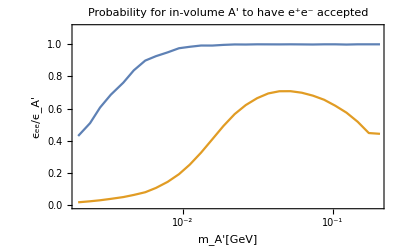

```mathematica
ListLinePlot[{datatracker,dataECAL},BaseStyle->{FontSize->14,FontFamily->"Times"},Frame->True,FrameLabel->{"m_A'[GeV]","ϵ_ee/ϵ_A'"},LabelStyle->{Black},FrameTicks->{{True, None},{myTicks[-3,0,1],None}},PlotRange->{{-2.7,-0.7},{0,1.1}},PlotLabel->"Probability for in-volume A' to have e^+e^- accepted",Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},{Style["Pass 3 trackers",10], Style["Enter ECAL",10]}]}],RoundingRadius->5],Scaled[{0.8,0.2}]] },ImageSize->400]
```

```mathematica
smallphotonrate= {Log[10,#1], #2} & @@@ Import[NotebookDirectory[]<>"ECAL.csv"][[2;;]]
smallopenrate= {Log[10,#1], #3} & @@@ Import[NotebookDirectory[]<>"ECAL.csv"][[2;;]]
```

{{-2.69897,0.0272053},{-2.61979,0.0353554},{-2.55284,0.0450131},{-2.48149,0.0564762},{-2.39794,0.0724936},{-2.3279,0.0917985},{-2.25181,0.11464},{-2.18046,0.148616},{-2.10237,0.198898},{-2.02687,0.257494},{-1.95468,0.334604},{-1.87943,0.424354},{-1.8041,0.524497},{-1.73049,0.618232},{-1.65561,0.711947},{-1.5817,0.780334},{-1.50585,0.840905},{-1.4318,0.882308},{-1.35754,0.913196},{-1.28316,0.934217},{-1.20831,0.950182},{-1.13371,0.963035},{-1.05948,0.973882},{-0.98464,0.984136},{-0.910095,0.989106},{-0.835647,0.994359},{-0.761201,0.997392},{-0.686766,1.},{-0.612077,1.}}

{{-2.69897,0.698167},{-2.61979,0.703777},{-2.55284,0.703715},{-2.48149,0.720387},{-2.39794,0.731711},{-2.3279,0.730129},{-2.25181,0.740604},{-2.18046,0.755142},{-2.10237,0.768538},{-2.02687,0.78952},{-1.95468,0.802642},{-1.87943,0.814428},{-1.8041,0.824205},{-1.73049,0.836692},{-1.65561,0.837915},{-1.5817,0.841059},{-1.50585,0.839563},{-1.4318,0.836888},{-1.35754,0.833037},{-1.28316,0.821597},{-1.20831,0.810295},{-1.13371,0.794614},{-1.05948,0.773716},{-0.98464,0.753505},{-0.910095,0.724331},{-0.835647,0.684997},{-0.761201,0.660784},{-0.686766,0.604317},{-0.612077,0.}}

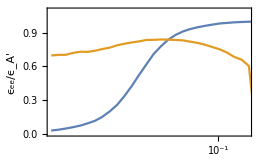

```mathematica
ListLinePlot[{smallphotonrate,smallopenrate},BaseStyle->{FontSize->14,FontFamily->"Times"},Frame->True,FrameLabel->{"m_A'[GeV]","ϵ_ee/ϵ_A'"},LabelStyle->{Black},FrameTicks->{{True, None},{myTicks[-3,0,1],None}},PlotRange->{{-2.7,-0.7},{0,1.1}},Image]
```

```mathematica
gamma2= Flatten[Log[10,#]  & @@@ Import[NotebookDirectory[]<>"2gamma.csv"]];
gamma20=Flatten[Log[10,#] & @@@Import[NotebookDirectory[]<>"20gamma.csv"]];
gamma200=Flatten[Log[10,#] & @@@Import[NotebookDirectory[]<>"200gamma.csv"]];
```

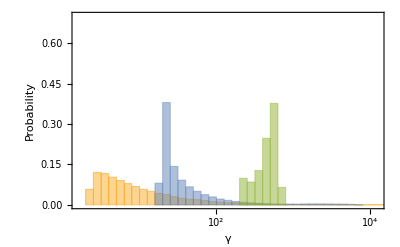

```mathematica
hist=Histogram[{gamma2,gamma20,gamma200},50,"Probability",PlotRange->{{0.2,4.1},{0,0.7}},ImageSize->400,BaseStyle->{FontSize->14,FontFamily->"Times"},Frame->True,FrameLabel->{"γ","Probability"},LabelStyle->{Black},FrameTicks->{{True,None},{myTicks[0,5,1],None}},Epilog->{Inset[Framed[Column[{SwatchLegend[{Directive[ColorData[97,2],Opacity[0.5]],Directive[ColorData[97,1],Opacity[0.5]],Directive[ColorData[97,3],Opacity[0.5]]},{Style["m_A' = 2 MeV", FontFamily->Times,FontSize->10],Style["m_A' = 20 MeV",FontFamily->Times,FontSize->10],Style["m_A' = 200 MeV",FontFamily->Times,FontSize->10]}]}],RoundingRadius->5],Scaled[{0.15,0.78}]] },ImageSize->400]
```

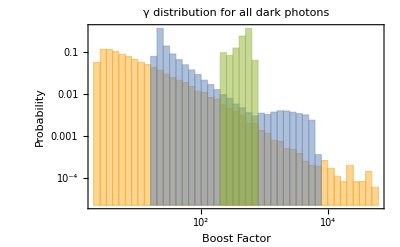

```mathematica
loghist=Histogram[{gamma2,gamma20,gamma200},50,"Probability",ScalingFunctions->"Log",PlotRange->{{0.2,4.8},{0,1}},ImageSize->400,BaseStyle->{FontSize->14,FontFamily->"Times"},PlotLabel->"γ distribution for all dark photons",Frame->True,FrameLabel->{"Boost Factor","Probability"},LabelStyle->{Black},FrameTicks->{{True,None},{myTicks[0,5,1],None}},Epilog->{Inset[Framed[Column[{SwatchLegend[{Directive[ColorData[97,2],Opacity[0.5]],Directive[ColorData[97,1],Opacity[0.5]],Directive[ColorData[97,3],Opacity[0.5]]},{Style["m_A' = 2 MeV", FontFamily->Times,FontSize->10],Style["m_A' = 20 MeV",FontFamily->Times,FontSize->10],Style["m_A' = 200 MeV",FontFamily->Times,FontSize->10]}]}],RoundingRadius->5],Scaled[{0.85,0.78}]] },ImageSize->400]
```

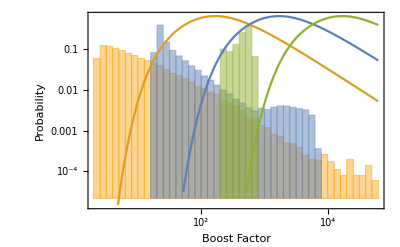

```mathematica
Show[loghist,decay1,decay2,decay3]
```

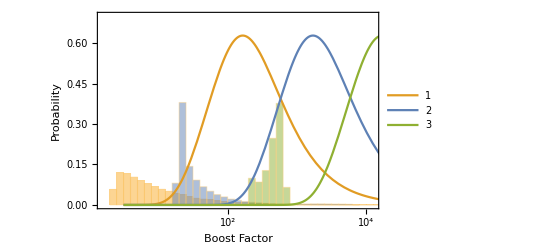

```mathematica
Show[hist,decay]
```